# Work Code Samples

## Starting Out: Elementary Arithmetic

### 1.1

```mathematica
1+2+3
```

6

### 1.2

```mathematica
1+2+3+4+5
```

15

### 1.3

```mathematica
1 2 3 4 5
```

120

### 1.4

```mathematica
5^2
```

25

### 1.5

```mathematica
3^4
```

81

### 1.6

```mathematica
10^12
```

1000000000000

### 1.7

```mathematica
3^(7 8)
```

523347633027360537213511521

### 1.8

```mathematica
(4-2)(3 +4)
```

14

### 1.9

```mathematica
29000 73
```

2117000

### +1.1

```mathematica
-3+-2+-1+0+1+2+3
```

0

### +1.2

```mathematica
24/3
```

8

### +1.3

```mathematica
5^100
```

7888609052210118054117285652827862296732064351090230047702789306640625

### +1.4

```mathematica
-5^2+100
```

75

```mathematica
100-5^2
```

75

### +1.5

```mathematica
6 5^2+7
```

157

### +1.6

```mathematica
3^2-2^3
```

1

### +1.7

```mathematica
2^3 3^2
```

72

### +1.8

```mathematica
2(8-11)
```

-6

## Introducing Functions

### 2.1

```mathematica
Plus[7,6,5]
```

18

### 2.2

```mathematica
Times[2,Plus[3,4]]
```

14

### 2.3

```mathematica
Max[6 8,5 9]
```

48

### 2.4

```mathematica
RandomInteger[1000]
```

797

```mathematica
RandomInteger[{0,1000}]
```

819

### 2.5

```mathematica
Plus[RandomInteger[10]+10]
```

20

### +2.1

```mathematica
Times[5,4,3,2]
```

120

### +2.2

```mathematica
Subtract[2,3]
```

-1

### +2.3

```mathematica
Times[Plus[8,7],Plus[9,2]]
```

165

### +2.4

```mathematica
Divide[Subtract[26,89],9]
```

-7

### +2.5

```mathematica
Subtract[100,Power[5,2]]
```

75

### +2.6

```mathematica
Max[3^5,5^3]
```

243

```mathematica
Max[Power[3,5],Power[5,3]]
```

243

### +2.7

```mathematica
Times[3,Max[Power[4,3],Power[3,4]]]
```

243

```mathematica
Times[3,Max[4^3,3^4]]
```

243

### +2.8

```mathematica
RandomInteger[1000]+RandomInteger[1000]
```

1253

## First Look at Lists

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

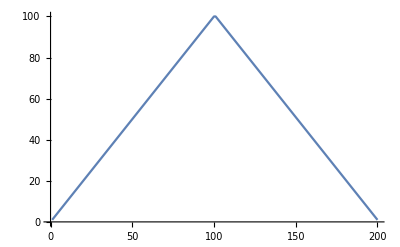

```mathematica
ListLinePlot[Join[Range[100],Reverse[Range[100]]]]
```

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Reverse[Reverse[Range[4]]]
```

{1,2,3,4}

```mathematica
Join[Range[5],Reverse[Range[4]]]
```

{1,2,3,4,5,4,3,2,1}

```mathematica
Join[Reverse[Range[3]],Reverse[Range[4]],Reverse[Range[5]]]
```

{3,2,1,4,3,2,1,5,4,3,2,1}

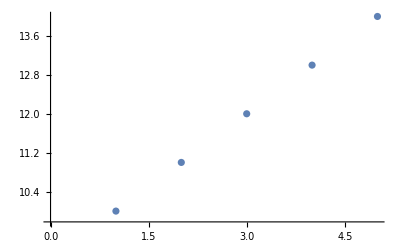

```mathematica
ListPlot[Range[10,14]]
```

```mathematica
Join[Range[10],Reverse[Range[10]],Range[10]]
```

{1,2,3,4,5,6,7,8,9,10,10,9,8,7,6,5,4,3,2,1,1,2,3,4,5,6,7,8,9,10}

## Displaying Lists

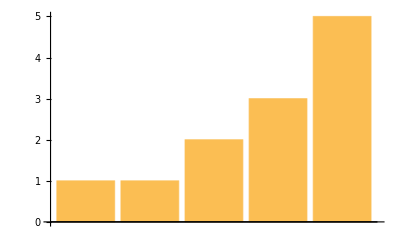

```mathematica
BarChart[{1,1,2,3,5}]
```

```mathematica
BarChart[Fibonacci[Range[5]]]
```

-Graphics-

```mathematica
PieChart[Range[10]]
```

-Graphics-

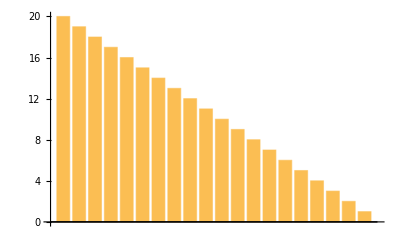

```mathematica
BarChart[Reverse[Range[20]]]
```

```mathematica
Column[Range[5]]
```

1
2
3
4
5

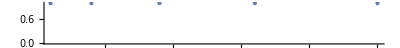

```mathematica
NumberLinePlot[{1,4,9,16,25}]
```

```mathematica
PieChart[{1,1,1,1,1,1,1,1,1,1}]
```

-Graphics-

```mathematica
Column[{PieChart[{1}],PieChart[{1,1}],PieChart[{1,1,1}]}]
```

-Graphics-

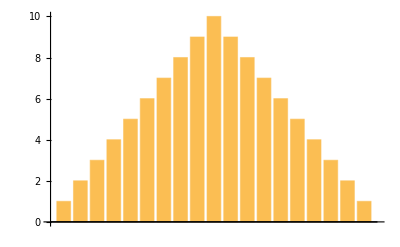

```mathematica
BarChart[Join[Range[10],Reverse[Range[9]]]]
```

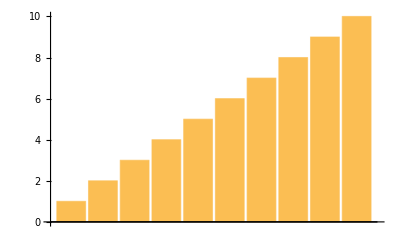
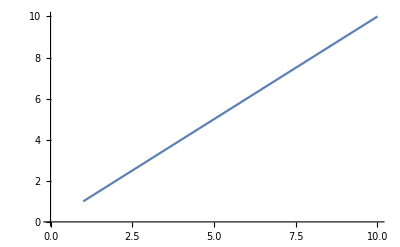
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{PieChart[Range[10]],BarChart[Range[10]],ListLinePlot[Range[10]]}
```

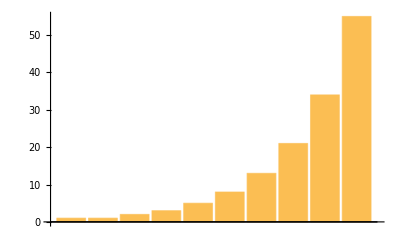
{-Graphics-,-Graphics-}

```mathematica
{PieChart[Fibonacci@Range[10]],BarChart[Fibonacci@Range[10]]}(*I can quickly produce the list {1,1,2,3,5,8,13,21,34,55} with Fibonacci@Range[10]*)
```

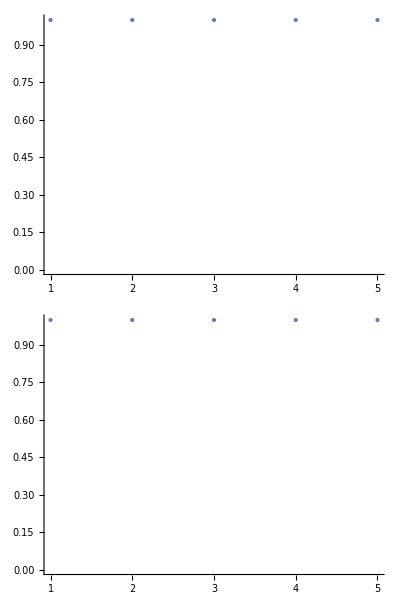

```mathematica
Column[{NumberLinePlot[Range[5]],NumberLinePlot[Range[5]]}]
```

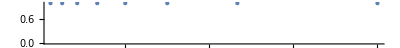

```mathematica
NumberLinePlot[1/Range[2,9]]
```

## Operations on Lists

### 5.1

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

### 5.2

```mathematica
Total[Range[10]^2]
```

385

### 5.3

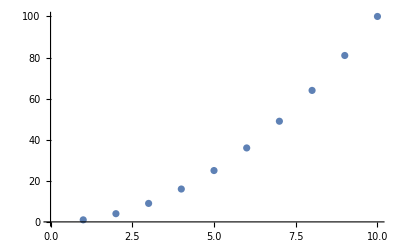

```mathematica
ListPlot[Range[10]^2]
```

### 5.4

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

### 5.5

```mathematica
Range[0,10]+10
```

{10,11,12,13,14,15,16,17,18,19,20}

### 5.6

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

### 5.7

```mathematica
Length[IntegerDigits[2^128]]
```

39

```mathematica
IntegerLength[2^128](*I can also use this built in function*)
```

39

### 5.8

```mathematica
First[IntegerDigits[2^32]]
```

4

### 5.9

```mathematica
Take[IntegerDigits[2^100]]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

### 5.10

```mathematica
Max[IntegerDigits[2^20]]
```

8

### 5.11

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

### 5.12

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

```mathematica
Sort[IntegerDigits[2^20]][[2]]
```

1

### 5.13

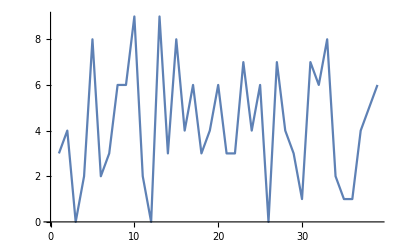

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

### 5.14

```mathematica
Drop[Take[Range[100],20],10]
```

{11,12,13,14,15,16,17,18,19,20}

### +5.1

```mathematica
3Range[10]
```

{3,6,9,12,15,18,21,24,27,30}

### +5.2

```mathematica
Times[Range[10],Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

### +5.3

```mathematica
Last[IntegerDigits[2^37]]
```

2

### +5.4

```mathematica
IntegerDigits[2^32][[-2]]
```

9

### +5.5

```mathematica
Total[IntegerDigits[3^126]]
```

234

### +5.6

```mathematica
PieChart[IntegerDigits[2^32]]
```

-Graphics-

### +5.7

```mathematica
{PieChart[IntegerDigits[2^20]],PieChart[IntegerDigits[2^40]],PieChart[IntegerDigits[2^60]]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Making Tables

### 6.1

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

### 6.2

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

### 6.3

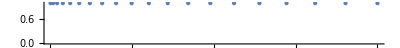

```mathematica
NumberLinePlot[Table[n^2,{n,20}]]
```

### 6.4

```mathematica
Table[2n,{n,10}]
```

{2,4,6,8,10,12,14,16,18,20}

### 6.5

```mathematica
Table[n,{n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

### 6.6

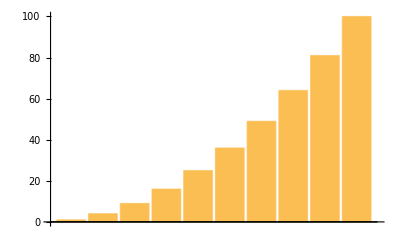

```mathematica
BarChart[Table[n^2,{n,10}]]
```

### 6.7

```mathematica
Table[IntegerDigits[n^2],{n,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

### 6.8

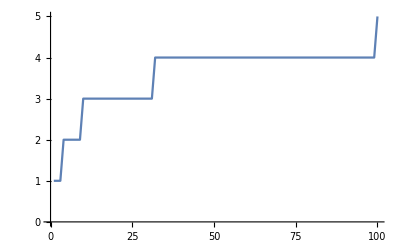

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

```mathematica
ListLinePlot[Table[IntegerLength[n^2],{n,100}]]
```

-Graphics-

### 6.9

```mathematica
Table[First[IntegerDigits[n^2]],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

### 6.10

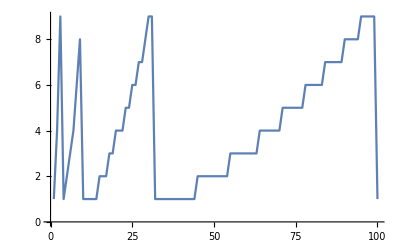

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,100}]]
```

### +6.1

```mathematica
Table[n^3-n^2,{n,10}]
```

{0,4,18,48,100,180,294,448,648,900}

### +6.2

```mathematica
Table[2n+1,{n,0,49}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

### +6.3

## Graphs and Networks

### +21.1

```mathematica
DirectedGraph@AdjacencyGraph[ConstantArray[1,{4,4}],GraphLayout->"RadialEmbedding"]
```

-Graphics-

### +21.7

```mathematica
CommunityGraphPlot[Graph[DirectedEdge@@@RandomInteger[100,{200,2}]]]
```

-Graphics-

## Machine Learning

### +22.1

```mathematica
ImageIdentify[Blur[Entity["Building","EiffelTower::5h9w8"]["Image"],#]]&/@Range[5]
```

{Eiffel Tower,Eiffel Tower,tower,stupa,stupa}

### +22.2

```mathematica
Classify["Sentiment",WikipediaData["happiness"]]
```

Neutral

### +22.3

```mathematica
Nearest[Table[Hue[h],{h,0,1,0.05}],Pink,3]
```

{Hue[0.9500000000000001],Hue[0.9],Hue[0.05]}

### +22.4

```mathematica
Nearest[Flatten[Table[i/j,{i,500},{j,500}]],Pi,10]
```

{355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155}

### +22.5

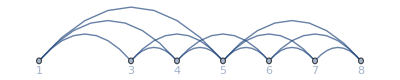

```mathematica
NearestNeighborGraph[RandomInteger[10,10],3,VertexLabels->Automatic]
```

### +22.6

```mathematica
FindClusters[RandomColor[100]]
```

{{RGBColor[0.1895725848174088, 0.4125524278815471, 0.21027103175866335],RGBColor[0.6160636883709314, 0.7376795954957682, 0.2743236621976277],RGBColor[0.3072866040867561, 0.4085638919245118, 0.042762228068248476],RGBColor[0.02336398412635332, 0.8056346377396397, 0.06571182463993952],RGBColor[0.05408310769886704, 0.9367582475768808, 0.09270325157260473],RGBColor[0.7794038777860284, 0.969029260210575, 0.10245389664970395],RGBColor[0.5607134661846433, 0.9361491753829017, 0.2929997274689764],RGBColor[0.09806967572418879, 0.5690043225300112, 0.22697899233501428],RGBColor[0.7603274899333103, 0.8235954343844538, 0.2039970984564674],RGBColor[0.4725027521168814, 0.6513113434229991, 0.07750335983760204],RGBColor[0.3527320367164226, 0.8258392341820708, 0.00323276014246332],RGBColor[0.31299787033106075, 0.5748658606804322, 0.18020945094594176],RGBColor[0.7033014657131256, 0.8419188544915046, 0.49862116985260285],RGBColor[0.669242039801957, 0.8816544877208734, 0.5632520346280132],RGBColor[0.569610208337777, 0.8481112302596843, 0.32098976642742105],RGBColor[0.44091492526818965, 0.42173866187910347, 0.055532151333284485],RGBColor[0.2203638427671204, 0.9190109511888953, 0.19569029420642825]},{RGBColor[0.5863700624326134, 0.15782113079391014, 0.8665045463260581],RGBColor[0.6670512797326251, 0.2406940815040426, 0.6084727441600049],RGBColor[0.24714028212677408, 0.3692837065749073, 0.8219233862379487],RGBColor[0.10688934562796737, 0.6192193943305331, 0.6147406656867762],RGBColor[0.3446074495415681, 0.4614339449456919, 0.8458879077335626],RGBColor[0.4713187848055169, 0.06165682757126567, 0.21980846256730313],RGBColor[0.3524585219222083, 0.7329243572517541, 0.8199627262339946],RGBColor[0.8254982913214617, 0.5865655597200856, 0.6501439229643651],RGBColor[0.0763165671512962, 0.33561714211339044, 0.42723406784740314],RGBColor[0.718538762253915, 0.22898236270749894, 0.818010696117164],RGBColor[0.5643500278729998, 0.17507814631144902, 0.8192170114775301],RGBColor[0.11894092767263609, 0.46091150565736627, 0.8114513609939857],RGBColor[0.1312315591339892, 0.33975420695201985, 0.9371946504698405],RGBColor[0.2158658201390946, 0.31309862129717314, 0.9490314243316178],RGBColor[0.7360343065897887, 0.12596436635148134, 0.194918759976197],RGBColor[0.21494517045029915, 0.12863047381536696, 0.5984184007805529],RGBColor[0.8086963097344133, 0.21264776351922965, 0.3979016010469347],RGBColor[0.6589485416809542, 0.3404264306713982, 0.2759954592846692],RGBColor[0.31347523848582814, 0.4173475557346642, 0.8891469301233248],RGBColor[0.4045275944770199, 0.24478665672394473, 0.955710864130042],RGBColor[0.9339852784664326, 0.6791175715322793, 0.596576627207283],RGBColor[0.8778681260367907, 0.03610999816556948, 0.44490411450852374],RGBColor[0.6718425461659678, 0.4982375968217838, 0.7290125190751937],RGBColor[0.02894294142751308, 0.3562490776177567, 0.7568361933349461],RGBColor[0.07970099760485372, 0.04775602233425413, 0.0370911560505629],RGBColor[0.4110777159780188, 0.21877493828473948, 0.7260111824003366],RGBColor[0.8369120047494625, 0.7379923634671088, 0.6922832232363756],RGBColor[0.9496409769210281, 0.2656283523255185, 0.36827584608042097],RGBColor[0.1555144904124841, 0.7429007094788393, 0.9918592997424833],RGBColor[0.29544082797615334, 0.36575282329973313, 0.6849193578595179],RGBColor[0.6243868711049114, 0.0721389292569421, 0.4552479616698879],RGBColor[0.6730676693003992, 0.28476733520906694, 0.4169697999952118],RGBColor[0.23357335961029313, 0.6227166084157312, 0.501804069204496],RGBColor[0.818578290404337, 0.4202258108801833, 0.4624973196478195],RGBColor[0.30289557190523486, 0.25821861530104306, 0.18284194033381018],RGBColor[0.2044003991585681, 0.3706844709648103, 0.6152096816118215],RGBColor[0.34394637964882535, 0.14438876491976327, 0.5567072519365148],RGBColor[0.490704352801254, 0.3061946843058072, 0.22146257230080924],RGBColor[0.9200561458548746, 0.9445483974253341, 0.937565157646054],RGBColor[0.15348674040981325, 0.3019211526578156, 0.8751734833483726],RGBColor[0.9544503623577751, 0.5659601353217583, 0.4271676718373698],RGBColor[0.983043172095919, 0.19334115952402686, 0.9890561319699238],RGBColor[0.4693183360625237, 0.6636224930177799, 0.8209294787713548],RGBColor[0.31732258295340743, 0.011848141880425489, 0.41333285406723785],RGBColor[0.5952599000086687, 0.45226228015756065, 0.8131132943506918],RGBColor[0.4984472048492796, 0.4998088224757813, 0.39574444808614717],RGBColor[0.8116140732009822, 0.6481555176024556, 0.8785544144325625],RGBColor[0.9685814420375123, 0.2631724533937343, 0.575854016067116],RGBColor[0.5043732320758822, 0.016799944319662474, 0.25801442801842156],RGBColor[0.9128543040594967, 0.33361074943185454, 0.8440726974834418],RGBColor[0.1467773823499241, 0.22463578720774735, 0.2500552683958581],RGBColor[0.08646412310852836, 0.6370162608788497, 0.5896241235945829],RGBColor[0.20287552745848103, 0.12374639502463358, 0.6721918969273224],RGBColor[0.41122709035464466, 0.5352673773614685, 0.8657440676079287],RGBColor[0.6284517340704645, 0.613251017557854, 0.6824831898088977],RGBColor[0.34199101241004315, 0.7943461158778113, 0.978552021920603],RGBColor[0.7292757935569405, 0.4337198815636383, 0.6176385631949066],RGBColor[0.3299893881459217, 0.36720423448409933, 0.7800528513172476],RGBColor[0.8915563244689766, 0.41224923956647563, 0.24547725636412898],RGBColor[0.14805008815690823, 0.047840709407043214, 0.6418274081051747],RGBColor[0.7918892112008062, 0.454006508499341, 0.3736597113026059],RGBColor[0.09734977879104356, 0.15560079478909428, 0.8216629852151243],RGBColor[0.715495251962784, 0.0342391402266633, 0.5229249127461768],RGBColor[0.18361835450930064, 0.5856413887821912, 0.9053564872739697],RGBColor[0.6444405500488712, 0.18182897360702044, 0.36688335645490944],RGBColor[0.7542875970099439, 0.5544439338790448, 0.9562639239211086],RGBColor[0.540407618506664, 0.4018941810625978, 0.7394231715171973],RGBColor[0.5290841080438216, 0.25050087212676053, 0.4750648421307524],RGBColor[0.05509973038292504, 0.3423987242814741, 0.5558238287910635],RGBColor[0.9853649227457115, 0.008949861533977588, 0.7240429308750886],RGBColor[0.5261458383794579, 0.31797414620331077, 0.28988066649046274],RGBColor[0.8911682720800416, 0.47027209342750154, 0.4520160352030014],RGBColor[0.49917334018563375, 0.125290511111384, 0.8405202443048554],RGBColor[0.9180789302732935, 0.09018487305622869, 0.3199538560839206],RGBColor[0.47052326677815404, 0.21211859366360297, 0.8610016862170022]},{RGBColor[0.839872922818713, 0.7287143892644756, 0.4815926922598113],RGBColor[0.9625665130521721, 0.8434498213496187, 0.6416723491124541],RGBColor[0.8204064329737808, 0.7508823123409691, 0.4444619734299129],RGBColor[0.8597468644595145, 0.733270799844659, 0.4139913178954]},{RGBColor[0.9054735885456124, 0.5299780187843961, 0.13222184798858772],RGBColor[0.8286617939933514, 0.5162922911557526, 0.07348135235242181]},{RGBColor[0.12496356122441998, 0.8862199266795556, 0.6347417595132903],RGBColor[0.05933424295028855, 0.8781372001113732, 0.5480608311526558]}}

### +22.7

```mathematica
FeatureSpacePlot[Rasterize/@Flatten[{#,ToUpperCase[#]}&/@Alphabet[]]]
```

-Graphics-

## More about Numbers

### +23.1

```mathematica
N[Pi,50]-Round[Pi]
```

0.141592653589793238462643383279502884197169399375

### +23.2

```mathematica
Sum[Prime[i],{i,1000}]
```

3682913

```mathematica
Total[Prime[Range[1000]]]
```

3682913

### +23.3

```mathematica
Mod[Prime[Range[100]],4]
```

{2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1}

### +23.4

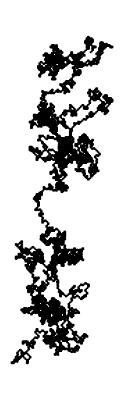

```mathematica
Graphics[Line[AnglePath[90° Mod[Prime[Range[10000]],4]]]]
```

## More Forms of Visualization

### +24.1

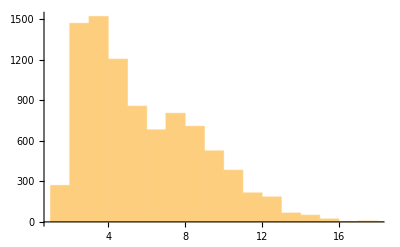

```mathematica
Histogram@StringLength[TextWords[WikipediaData["computers"]]]
```

## Pure Anonymous Functions

### +26.1

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

## Applying Functions Repeatedly

### +27.1

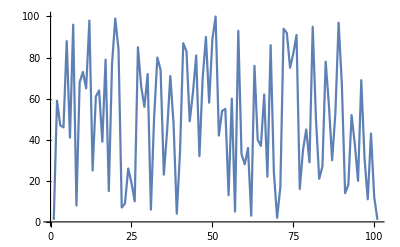

```mathematica
ListLinePlot[NestList[Mod[59#,101]&,1,100]]
```

### +27.2

```mathematica
NestList[2^#&,1,4]
```

{1,2,4,16,65536}

### +27.3

```mathematica
NestList[1.2^#&,0,19]
```

{0,1.,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}

### +27.4

```mathematica
NestList[Sqrt[1+#]&,1,10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

### +27.5

```mathematica
Graphics3D[Line[NestList[RandomReal[{-1,1},3]+#&,{0,0,0},1000]]]
```

-Graphics3D-

## Tests and Conditions

### +28.1

```mathematica
Table[If[Last[IntegerDigits[i]]==3,0,i],{i,25}]
```

{1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25}

### +28.2

```mathematica
Table[If[i==j,1,0],{i,5},{j,5}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

### +28.3

```mathematica
Select[Mod[#,7]==1&][Select[Mod[#,8]==1&][Range[1000]]]
```

{1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953}

### +28.4

```mathematica
Table[If[Mod[i,3]==Mod[i,5]==0,Red,If[Mod[i,3]==0,Black,If[Mod[i,5]==0,White,i]]],{i,100}]
```

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

### +28.5

```mathematica
Select[#["Mass"]
>Entity["Planet","Earth"]["Mass"]&][EntityList["Planet"]]
```

{Jupiter,Saturn,Uranus,Neptune}

### +28.6

```mathematica
ArrayPlot[Table[If[Mod[i,j]==0,1,0],{i,50},{j,50}]]
```

-Graphics-

### +28.6

```mathematica
ArrayPlot[Table[If[AllTrue[IntegerDigits/@{i,j},FreeQ[5]],1,0],{i,100},{j,100}]]
```

-Graphics-

## More about Pure Functions

### +29.1

```mathematica
Array[If[#1>=#2,1,0]&,{10,10}]//Grid
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

## Rearranging Lists

### 30.1

```mathematica
Thread[Alphabet[]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

### 30.2

```mathematica
Grid[Partition[Alphabet[],6]]
```

a | b | c | d | e | f
g | h | i | j | k | l
m | n | o | p | q | r
s | t | u | v | w | x

### 30.3

```mathematica
Grid[Partition[IntegerDigits[2^1000],50],Frame->All]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

### 30.4

```mathematica
WikipediaData["computers"]//Characters//Take[#,400]&//Partition[#,20]&//Grid[#,Frame->All]&
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | d | i | g | i
t | a | l |   | e | l | e | c | t | r | o | n | i | c |   | m | a | c | h | i
n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | p | r | o | g | r
a | m | m | e | d |   | t | o |   | c | a | r | r | y |   | o | u | t |   | s
e | q | u | e | n | c | e | s |   | o | f |   | a | r | i | t | h | m | e | t
i | c |   | o | r |   | l | o | g | i | c | a | l |   | o | p | e | r | a | t
i | o | n | s |   | ( | c | o | m | p | u | t | a | t | i | o | n | ) |   | a
u | t | o | m | a | t | i | c | a | l | l | y | . |   | M | o | d | e | r | n
  | c | o | m | p | u | t | e | r | s |   | c | a | n |   | p | e | r | f | o
r | m |   | g | e | n | e | r | i | c |   | s | e | t | s |   | o | f |   | o
p | e | r | a | t | i | o | n | s |   | k | n | o | w | n |   | a | s |   | p
r | o | g | r | a | m | s | . |   | T | h | e | s | e |   | p | r | o | g | r
a | m | s |   | e | n | a | b | l | e |   | c | o | m | p | u | t | e | r | s
  | t | o |   | p | e | r | f | o | r | m |   | a |   | w | i | d | e |   | r
a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | A |   | c | o | m
p | u | t | e | r |   | s | y | s | t | e | m |   | i | s |   | a |   | " | c
o | m | p | l | e | t | e | " |   | c | o | m | p | u | t | e | r |   | t | h
a | t |   | i | n | c | l | u | d | e | s |   | t | h | e |   | h | a | r | d
w | a | r | e | , |   | o | p | e | r | a | t | i | n | g |   | s | y | s | t
e | m |   | ( | m | a | i | n |   | s | o | f | t | w | a | r | e | ) | , |

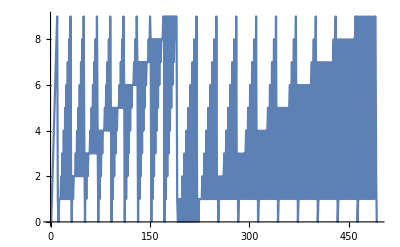

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[0,200]]]]
```


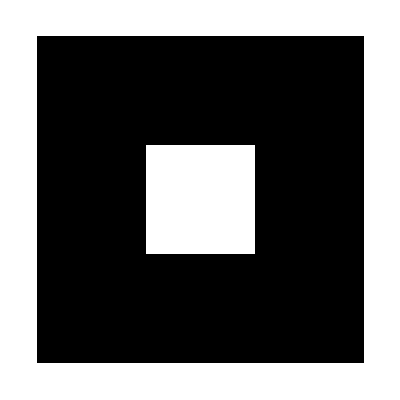
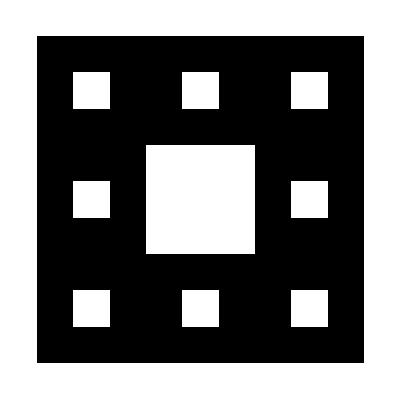
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]
```

```mathematica
Function[x,Join[x,{Sqrt[Total[#^2&/@x]]}]]/@Select[Function[x,IntegerQ[Sqrt[Total[#^2&/@x]]]]][Tuples[Range[20],{2}]]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

```mathematica
Max[Length/@Split[IntegerDigits[2^#]]]&/@Range[100]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
GatherBy[IntegerName/@Range[100],StringTake[#,1]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
SortBy[Take[WordList[],50],StringDrop[#,-1]&]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abash,abasement,abashed,abashment,abate,abatement,abattoir,abbe,abbey,abbess,abbot,abbreviate,abbreviated,abbreviation,abdicate,abdication,abdomen,abdominal,abduct,abducting,abduction,abductor,abed,abet,abeam,aberrant,aberration,abettor,abeyance,abhor,abhorrent,abhorrence,abide,abidance,abiding,ability,abject,abjection,abjectly}

```mathematica
SortBy[Take[WordList[],50],StringPart[#,-1]&]
```

{a,abandoned,abashed,abbreviated,abed,abalone,abase,abate,abbe,abbreviate,abdicate,abeyance,abhorrence,abidance,abide,abducting,abiding,aah,abash,aardvark,aback,abdominal,abeam,abandon,abbreviation,abdication,abdomen,abduction,aberration,abjection,abattoir,abductor,abettor,abhor,abacus,abbess,abaft,abandonment,abasement,abashment,abatement,abbot,abduct,aberrant,abet,abhorrent,abject,abbey,ability,abjectly}

```mathematica
Range[20]^2
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
SortBy[First[IntegerDigits[#]]&][Range[20]^2]
```

{1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9}

```mathematica
SortBy[StringLength[IntegerName[#,"English"]]&][Range[20]]
```

{1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17}

```mathematica
GatherBy[RandomSample[WordList[],20],StringLength]
```

{{expositor,promotion,lustiness,healthier},{nerd,oxen,taps},{shove,gumbo},{tablecloth,isometrics},{rescind,bizarre},{apprehension,ossification,masterstroke},{dwarfish},{businesspeople},{tinker},{incarcerate}}

```mathematica
Complement[Alphabet["Ukrainian"],Alphabet["Russian"]]
```

{є,і,ї,ґ}

```mathematica
Intersection[Range[100]^2,Range[100]^3]
```

{1,64,729,4096}

```mathematica
EntityList[IntersectedEntityClass[,EntityClass["Country","GroupOf8"]]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
Grid@Transpose[Permutations[Range[4]]]
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
Transpose[Permutations[Range[4]]]//Grid
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
Sort[StringJoin/@Permutations[Characters["hello"]]]
```

{ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,lehlo,lehol,lelho,leloh,leohl,leolh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lleho,lleoh,llheo,llhoe,lloeh,llohe,loehl,loelh,lohel,lohle,loleh,lolhe,oehll,oelhl,oellh,ohell,ohlel,ohlle,olehl,olelh,olhel,olhle,olleh,ollhe}

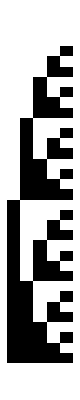

```mathematica
ArrayPlot[Tuples[{0,1},5]]
```

```mathematica
StringJoin/@RandomChoice[Alphabet[],{10,5}]
```

{rqtwv,kjlmy,wxszw,mioko,ycrwe,yimln,htily,sstlb,sbxie,onmhr}

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
PacletInstall["Wolfram/CodeEquivalenceUtilities"]
```

PacletObject[…]

```mathematica
Needs["Wolfram`CodeEquivalenceUtilities`"]
```

```mathematica
EquivalenceTestData[SortBy[Range[20],StringLength[IntegerName[#]]&],SortBy[StringLength[IntegerName[#]]&][Range[20]]]
```

<|Timing→<|SameQ→0.,EqualQ→0.0009722,ToCanonicalForm1→0.0488236,ToCanonicalForm2→0.7597095|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[SortBy[Table[𝓈_1∷ℤ,{𝓈_1∷ℤ,1,20,1}],StringLength[IntegerName[#1]]&]],2→HoldComplete[SortBy[Table[𝓈_1∷ℤ,{𝓈_1∷ℤ,1,20,1}],StringLength[IntegerName[#1]]&]]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

```mathematica
EquivalenceTestData[SortBy[Range[20],StringLength[IntegerName[#]]&],SortBy[StringLength[IntegerName[#]]&][Range[20]]]
```

<|Timing→<|SameQ→0.,EqualQ→0.0009722,ToCanonicalForm1→0.0488236,ToCanonicalForm2→0.7597095|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[SortBy[Table[𝓈_1∷ℤ,{𝓈_1∷ℤ,1,20,1}],StringLength[IntegerName[#1]]&]],2→HoldComplete[SortBy[Table[𝓈_1∷ℤ,{𝓈_1∷ℤ,1,20,1}],StringLength[IntegerName[#1]]&]]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

### +30.1

```mathematica
Partition[LetterNumber[Select[LetterQ]@Take[Characters[WikipediaData["computers"]],1000]],30]//ArrayPlot
```

-Graphics-

### +30.2

```mathematica
GatherBy[Range[30],Mod[#,3]&]
```

{{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}}

### +30.3

```mathematica
GatherBy[2^Range[50],Last[IntegerDigits[#]]&]
```

{{2,32,512,8192,131072,2097152,33554432,536870912,8589934592,137438953472,2199023255552,35184372088832,562949953421312},{4,64,1024,16384,262144,4194304,67108864,1073741824,17179869184,274877906944,4398046511104,70368744177664,1125899906842624},{8,128,2048,32768,524288,8388608,134217728,2147483648,34359738368,549755813888,8796093022208,140737488355328},{16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776,17592186044416,281474976710656}}

### +30.4

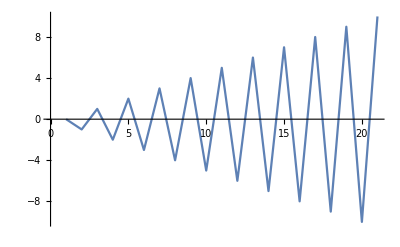

```mathematica
ListLinePlot[SortBy[Range[-10,10],Abs]]
```

### +30.5

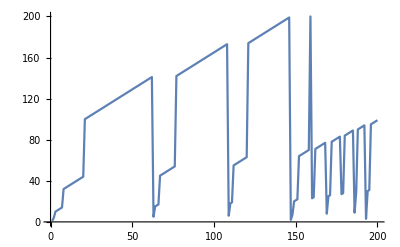

```mathematica
ListLinePlot[SortBy[First[IntegerDigits[#^2]]&][Range[200]]]
```

### +30.6

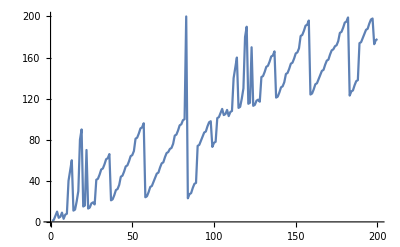

```mathematica
ListLinePlot[SortBy[StringLength[IntegerName[#]]&][Range[200]]]
```

### +30.7

```mathematica
RandomSample[WordList[],25]
```

{whew,shoreward,dauntingly,dribbling,anchorite,perform,fontanel,repudiate,encourage,insurgency,nucleated,elf,toilette,untimeliness,unilateralism,panting,hypnotist,indexer,fern,banquet,lineally,metaphysics,savvy,paramagnetism,cormorant}

### +30.8

```mathematica
StringRiffle[Characters@"UNCLE","."]
```

U.N.C.L.E

### +30.9

```mathematica
Complement[Join[Alphabet["Swedish"],Alphabet["Polish"]],Alphabet["English"]]
```

{ą,ę,ń,ś,ź,ż,å,ä,ć,ł,ó,ö}

### +30.10

```mathematica
Complement[EntityList@EntityClass["Country","WorldHealthOrganization"],EntityList@EntityClass["Country","UnitedNations"]]
```

{Cook Islands,Niue}

```mathematica
EntityList[
ComplementedEntityClass[EntityClass["Country","WorldHealthOrganization"],EntityClass["Country","UnitedNations"]]]
```

{Cook Islands,Niue}

### +30.11

```mathematica
Blend/@Tuples[{Red,Green,Blue},2]
```

{RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]}

### +30.12

```mathematica
ArrayPlot/@Partition[Tuples[{0,1},8],50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### +30.13

```mathematica
Intersection[WordList[],StringJoin/@RandomChoice[Alphabet[],{1000,4}]]
```

{free}

## Parts of Lists

### 31.1

```mathematica
IntegerDigits[2^1000][[-5;;-1]]
```

{6,9,3,7,6}

### 31.2

```mathematica
Alphabet[][[10;;20]]
```

{j,k,l,m,n,o,p,q,r,s,t}

### 31.3

```mathematica
Alphabet[][[2;;;;2]]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

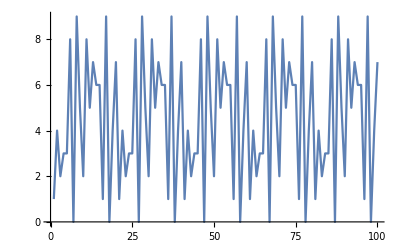

```mathematica
ListLinePlot[IntegerDigits[12^#][[-2]]&/@Range[100]]
```

### 31.4

### 31.5

## Patterns

```mathematica
Cases[IntegerDigits@Range[1000],{1,_,9}]
```

{{1,0,9},{1,1,9},{1,2,9},{1,3,9},{1,4,9},{1,5,9},{1,6,9},{1,7,9},{1,8,9},{1,9,9}}

```mathematica
Cases[IntegerDigits@Range[1000],{b_,b_,b_}]
```

{{1,1,1},{2,2,2},{3,3,3},{4,4,4},{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]^2],{9,___,0|1}]
```

{{9,0,0},{9,6,1},{9,8,0,1},{9,0,0,0,0},{9,0,6,0,1},{9,5,4,8,1},{9,6,1,0,0},{9,6,7,2,1},{9,0,0,6,0,1},{9,0,2,5,0,0},{9,0,4,4,0,1},{9,1,9,6,8,1},{9,2,1,6,0,0},{9,2,3,5,2,1},{9,3,8,9,6,1},{9,4,0,9,0,0},{9,4,2,8,4,1},{9,5,8,4,4,1},{9,6,0,4,0,0},{9,6,2,3,6,1},{9,7,8,1,2,1},{9,8,0,1,0,0},{9,8,2,0,8,1},{9,9,8,0,0,1}}

```mathematica
IntegerDigits[Range[100]]/.{0->Gray,9->Orange}
```

{{1},{2},{3},{4},{5},{6},{7},{8},{RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5]},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,RGBColor[1, 0.5, 0]},{2,GrayLevel[0.5]},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,RGBColor[1, 0.5, 0]},{3,GrayLevel[0.5]},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,RGBColor[1, 0.5, 0]},{4,GrayLevel[0.5]},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,RGBColor[1, 0.5, 0]},{5,GrayLevel[0.5]},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,RGBColor[1, 0.5, 0]},{6,GrayLevel[0.5]},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,RGBColor[1, 0.5, 0]},{7,GrayLevel[0.5]},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,RGBColor[1, 0.5, 0]},{8,GrayLevel[0.5]},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,RGBColor[1, 0.5, 0]},{RGBColor[1, 0.5, 0],GrayLevel[0.5]},{RGBColor[1, 0.5, 0],1},{RGBColor[1, 0.5, 0],2},{RGBColor[1, 0.5, 0],3},{RGBColor[1, 0.5, 0],4},{RGBColor[1, 0.5, 0],5},{RGBColor[1, 0.5, 0],6},{RGBColor[1, 0.5, 0],7},{RGBColor[1, 0.5, 0],8},{RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5],GrayLevel[0.5]}}

```mathematica
IntegerDigits[2^1000]/.{0->Red}
```

{1,RGBColor[1, 0, 0],7,1,5,RGBColor[1, 0, 0],8,6,RGBColor[1, 0, 0],7,1,8,6,2,6,7,3,2,RGBColor[1, 0, 0],9,4,8,4,2,5,RGBColor[1, 0, 0],4,9,RGBColor[1, 0, 0],6,RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],1,8,1,RGBColor[1, 0, 0],5,6,1,4,RGBColor[1, 0, 0],4,8,1,1,7,RGBColor[1, 0, 0],5,5,3,3,6,RGBColor[1, 0, 0],7,4,4,3,7,5,RGBColor[1, 0, 0],3,8,8,3,7,RGBColor[1, 0, 0],3,5,1,RGBColor[1, 0, 0],5,1,1,2,4,9,3,6,1,2,2,4,9,3,1,9,8,3,7,8,8,1,5,6,9,5,8,5,8,1,2,7,5,9,4,6,7,2,9,1,7,5,5,3,1,4,6,8,2,5,1,8,7,1,4,5,2,8,5,6,9,2,3,1,4,RGBColor[1, 0, 0],4,3,5,9,8,4,5,7,7,5,7,4,6,9,8,5,7,4,8,RGBColor[1, 0, 0],3,9,3,4,5,6,7,7,7,4,8,2,4,2,3,RGBColor[1, 0, 0],9,8,5,4,2,1,RGBColor[1, 0, 0],7,4,6,RGBColor[1, 0, 0],5,RGBColor[1, 0, 0],6,2,3,7,1,1,4,1,8,7,7,9,5,4,1,8,2,1,5,3,RGBColor[1, 0, 0],4,6,4,7,4,9,8,3,5,8,1,9,4,1,2,6,7,3,9,8,7,6,7,5,5,9,1,6,5,5,4,3,9,4,6,RGBColor[1, 0, 0],7,7,RGBColor[1, 0, 0],6,2,9,1,4,5,7,1,1,9,6,4,7,7,6,8,6,5,4,2,1,6,7,6,6,RGBColor[1, 0, 0],4,2,9,8,3,1,6,5,2,6,2,4,3,8,6,8,3,7,2,RGBColor[1, 0, 0],5,6,6,8,RGBColor[1, 0, 0],6,9,3,7,6}

```mathematica
Characters["The Wolfram Language"]/.{"a"|"e"|"i"|"o"|"u"->Nothing}
```

{T,h, ,W,l,f,r,m, ,L,n,g,g}

```mathematica
Cases[0|1][IntegerDigits[2^1000]]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Cases[{b_,___,b_}][IntegerDigits[Range[100,999]]]
```

{{1,0,1},{1,1,1},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{2,0,2},{2,1,2},{2,2,2},{2,3,2},{2,4,2},{2,5,2},{2,6,2},{2,7,2},{2,8,2},{2,9,2},{3,0,3},{3,1,3},{3,2,3},{3,3,3},{3,4,3},{3,5,3},{3,6,3},{3,7,3},{3,8,3},{3,9,3},{4,0,4},{4,1,4},{4,2,4},{4,3,4},{4,4,4},{4,5,4},{4,6,4},{4,7,4},{4,8,4},{4,9,4},{5,0,5},{5,1,5},{5,2,5},{5,3,5},{5,4,5},{5,5,5},{5,6,5},{5,7,5},{5,8,5},{5,9,5},{6,0,6},{6,1,6},{6,2,6},{6,3,6},{6,4,6},{6,5,6},{6,6,6},{6,7,6},{6,8,6},{6,9,6},{7,0,7},{7,1,7},{7,2,7},{7,3,7},{7,4,7},{7,5,7},{7,6,7},{7,7,7},{7,8,7},{7,9,7},{8,0,8},{8,1,8},{8,2,8},{8,3,8},{8,4,8},{8,5,8},{8,6,8},{8,7,8},{8,8,8},{8,9,8},{9,0,9},{9,1,9},{9,2,9},{9,3,9},{9,4,9},{9,5,9},{9,6,9},{9,7,9},{9,8,9},{9,9,9}}

## Creating Websites and Apps

### +36.1

```mathematica
CloudDeploy[Delayed[Graphics[{Red,RegularPolygon[RandomInteger[{3,8}]]}]],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/1730a927-ab52-45b5-a431-1c884c8b0703]

### +36.2

```mathematica
CloudDeploy[FormFunction[<|"x"->"SemanticNumber","y"->"SemanticNumber"|>,(#x)^(#y)&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/498da17a-a87c-4583-9ba6-c7dbc558b278]

Display the prime factorization of an integer:

```mathematica
CenterDot@@Superscript@@@FactorInteger[2002!]
```

2^1995·3^997·5^499·7^331·11^199·13^165·17^123·19^110·23^90·29^71·31^66·37^55·41^49·43^47·47^42·53^37·59^33·61^32·67^29·71^28·73^27·79^25·83^24·89^22·97^20·101^19·103^19·107^18·109^18·113^17·127^15·131^15·137^14·139^14·149^13·151^13·157^12·163^12·167^11·173^11·179^11·181^11·191^10·193^10·197^10·199^10·211^9·223^8·227^8·229^8·233^8·239^8·241^8·251^7·257^7·263^7·269^7·271^7·277^7·281^7·283^7·293^6·307^6·311^6·313^6·317^6·331^6·337^5·347^5·349^5·353^5·359^5·367^5·373^5·379^5·383^5·389^5·397^5·401^4·409^4·419^4·421^4·431^4·433^4·439^4·443^4·449^4·457^4·461^4·463^4·467^4·479^4·487^4·491^4·499^4·503^3·509^3·521^3·523^3·541^3·547^3·557^3·563^3·569^3·571^3·577^3·587^3·593^3·599^3·601^3·607^3·613^3·617^3·619^3·631^3·641^3·643^3·647^3·653^3·659^3·661^3·673^2·677^2·683^2·691^2·701^2·709^2·719^2·727^2·733^2·739^2·743^2·751^2·757^2·761^2·769^2·773^2·787^2·797^2·809^2·811^2·821^2·823^2·827^2·829^2·839^2·853^2·857^2·859^2·863^2·877^2·881^2·883^2·887^2·907^2·911^2·919^2·929^2·937^2·941^2·947^2·953^2·967^2·971^2·977^2·983^2·991^2·997^2·1009^1·1013^1·1019^1·1021^1·1031^1·1033^1·1039^1·1049^1·1051^1·1061^1·1063^1·1069^1·1087^1·1091^1·1093^1·1097^1·1103^1·1109^1·1117^1·1123^1·1129^1·1151^1·1153^1·1163^1·1171^1·1181^1·1187^1·1193^1·1201^1·1213^1·1217^1·1223^1·1229^1·1231^1·1237^1·1249^1·1259^1·1277^1·1279^1·1283^1·1289^1·1291^1·1297^1·1301^1·1303^1·1307^1·1319^1·1321^1·1327^1·1361^1·1367^1·1373^1·1381^1·1399^1·1409^1·1423^1·1427^1·1429^1·1433^1·1439^1·1447^1·1451^1·1453^1·1459^1·1471^1·1481^1·1483^1·1487^1·1489^1·1493^1·1499^1·1511^1·1523^1·1531^1·1543^1·1549^1·1553^1·1559^1·1567^1·1571^1·1579^1·1583^1·1597^1·1601^1·1607^1·1609^1·1613^1·1619^1·1621^1·1627^1·1637^1·1657^1·1663^1·1667^1·1669^1·1693^1·1697^1·1699^1·1709^1·1721^1·1723^1·1733^1·1741^1·1747^1·1753^1·1759^1·1777^1·1783^1·1787^1·1789^1·1801^1·1811^1·1823^1·1831^1·1847^1·1861^1·1867^1·1871^1·1873^1·1877^1·1879^1·1889^1·1901^1·1907^1·1913^1·1931^1·1933^1·1949^1·1951^1·1973^1·1979^1·1987^1·1993^1·1997^1·1999^1

```mathematica
Map[f,{{a,b,c},{x,y,z}}]
```

{f[{a,b,c}],f[{x,y,z}]}

```mathematica
Map[f,{{a,b,c},{x,y,z}},{1}]
```

{f[{a,b,c}],f[{x,y,z}]}

```mathematica
Map[f,{{a,b,c},{x,y,z}},{2}]
```

{{f[a],f[b],f[c]},{f[x],f[y],f[z]}}

```mathematica
MapThread[f,{{a,b,c},{x,y,z}}]
```

{f[a,x],f[b,y],f[c,z]}